基礎庫 :

```mathematica
<<(FileNameJoin[{$UserDocumentsDirectory,"Wolfram Mathematica","snslib.wl"}])
```

WorkPath :

```mathematica
SetDirectory["D:\\Work\\SSR\\basePlan"];
dataPath = FileNameJoin[{ParentDirectory[],"_data"}]
```

D:\Work\SSR\_data

```mathematica
Config :
```

```mathematica
ClearAll[resconfig,baseconfig,relyconfig,baseRely,weightconfig,bdweight,bdKeys,resWeight];
resconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"resource","base"];
baseconfig =Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"build","base"];
relyconfig = Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"build","rely"];
baseRely[from_,to_]:= Merge[Max]@MapThread[AssociationThread[#2->#1]&,{Range[from,to],Normal@relyconfig[Range[from,to],{"q1","q2","q3"},StringSplit[#,","]&][All,Flatten@Values[#]&]}];
baseRely[lv_]:= AssociationThread[Flatten@Normal@Values@relyconfig[lv,{"q1","q2","q3"},StringSplit[#,","]&]->lv];
weightconfig= Base`excleData[FileNameJoin[{Directory[],"main.xlsx"}],"build","weight"];
bdweight[key_String] :=  Base`excleLookUp[weightconfig,"key"-> key,"value"];
bdweight[key_String,res_String]:= bdweight[key]*Base`excleLookUp[weightconfig,"key"-> key,res]/Total[Base`excleLookUp[weightconfig,"key"-> key,{"r1","r2","r3"}]];
bdKeys = weightconfig[All,"key"];
resWeight = <|"r1"-> (bdweight[#,"r1"]&/@bdKeys),"r2"-> (bdweight[#,"r2"]&/@bdKeys),"r3"-> (bdweight[#,"r3"]&/@bdKeys)|>;
```

## 升级时间

```mathematica
ClearAll[relybdTime,speedLvData,bdTimeKey,bdTime,bdTimeInfo,bdTimefuncs,x];
speedLvData= SemanticImport[FileNameJoin[{dataPath,"speedLvInfo.txt"}]];
relybdTime[lv_]:= If[Length@baseRely[lv]>0, AssociationThread[Keys@baseRely[lv]->(#2*#1/Total[#1]&)[bdweight[#]&/@Keys@baseRely[lv],speedLvData[SelectFirst[#Lv==lv&],"relyTime"]]],<||>];
bdTimeKey[key_]:= Module[{data=Select[Table[{n,If[KeyExistsQ[relybdTime[n],key],Part[#,key]&@relybdTime[n],Missing[]]},{n,1,35}],!MissingQ[Last@#]&]},MapThread[{First[#1],Last@#1*2/(First[#1]-#2+1)}&,{data,Prepend[First/@data[[;;-2]],0]}]];
bdTimefuncs =   (#->Normal@NonlinearModelFit[bdTimeKey[#],a*E^(b*x),{a,b},x])&/@baseconfig[2;;,"key"];
bdTime[key_/;key≠ "base",lv_/;lv≥ 7]:= (Association@@bdTimefuncs)[key]/.x->lv;
bdTime[key_/;key== "base",lv_]:= SemanticImport[FileNameJoin[{dataPath,"speedLvInfo.txt"}]][lv,"mainTime"];
bdTime[key_/;key≠  "base",lv_/;lv< 7]:= lv^2*bdTime["base",lv]*bdweight[key]/bdweight["base"];
bdTimeInfo[lv_]:=AssociationThread[Normal@baseconfig[2;;,"key"]-> Normal@(bdTime[#,lv]&/@baseconfig[2;;,"key"])];
```

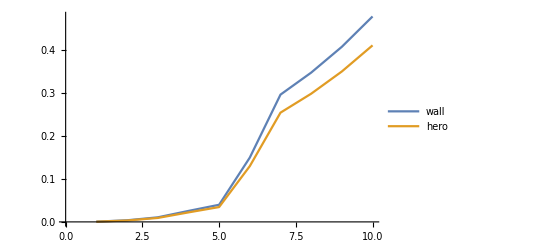

```mathematica
ListLinePlot[Transpose@Table[{bdTime["wall",n],bdTime["hero",n]},{n,1,10}],PlotLegends->{"wall","hero"}]
```

## 建筑链

main.xlsx -> build -> rely

```mathematica
ClearAll[relyBuilding];
relyBuilding[key_,lv_/;lv==1]:=""; 
relyBuilding[key_/;key=="base",lv_/;lv>1]:= Module[{other = StringForm["building_``_``",#,lv]&/@DeleteMissing@Normal[relyconfig[lv,{"q1","q2","q3"},StringSplit[#,","]&][Values,First]]},StringRiffle[other,";"]];
relyBuilding[key_/;key≠ "base",lv_/;lv>1]:=Module[{data=DeleteCases[Normal@relyconfig[All,"other",StringSplit[#,","]&],{}],base=ToString@StringForm["building_base_``",lv]},If[MemberQ[First/@data,key],StringRiffle[Prepend[StringForm["building_``_``",#,lv]&/@SelectFirst[data,First@#==key&][[2;;]],base],";"],base]];
```

## Data导出

D:\WorkPath\k-config\trunk\excel\building_data.xlsx

```mathematica
ClearAll[bdData];
bdData[key_String,lv_]:= <|"stringId"-> ToString@StringForm["building_``_``",key,lv],"note"-> baseconfig[SelectFirst[#key==key&],"name"]<>"lv"<>ToString@lv,"buildingID"->"building_"<>key,"lv"->lv,"appearanceID"-> "bd_appearance_"<>key,"time"-> dayToDuration@bdTime[key,lv],"itemgroup"->ToString@StringForm["consume_building_``_``",key,lv],"depend"-> relyBuilding[key,lv],"attrgroupId"-> ToString@StringForm["attr_building_``_``",key,lv]|>;
```

```mathematica
Export[FileNameJoin[{dataPath,"building_data.txt"}],Dataset[Flatten@Outer[bdData,Normal@baseconfig[All,"key"],Range[maxLv]]],"Table"]
```

D:\Work\SSR\_data\building_data.txt

## 资源消耗

D:\WorkPath\k-config\trunk\excel\itemgroup.xlsx

```mathematica
ClearAll[resConsumeData,bdConsume,consumeData];
resConsumeData = Association@@(#-> Normal@SemanticImport[FileNameJoin[{dataPath,#<>"_"<>"consumeData.txt"}]][All,"build"]&/@{"r1","r2","r3"});
bdConsume[key_String,res_String,lv_]:=Module[{consume=resConsumeData[res][[lv]]},Round[consume*bdweight[key,res]/Total[resWeight[res]],10]];
bdConsume[key_String,lv_]:=DeleteCases[Base`excleLookUp[resconfig,"type"->#,"item"]->bdConsume[key,#,lv]&/@{"r1","r2","r3"},x_/;Values[x]==0];
consumeData[key_String,lv_]:= snsItemgroup[ToString@StringForm["consume_building_``_``",key,lv]->Association@@bdConsume[key,lv]];
```

```mathematica
snsExportTable["itemgroup-build.csv",snsUpdateTable["itemgroup-build.csv",Association@@Flatten@Outer[consumeData,Normal@baseconfig[All,"key"],Range[maxLv-1]]]]
```

C:\k-config\excel\itemgroup-build.csv

```mathematica
consumeData["base",1]
```

<|consume_building_base_1→<|道具0→item_rA,数量0→10,权重0→1,产出数量→1,道具1→,道具2→,道具3→,道具4→,道具5→,道具6→,道具7→,道具8→,道具9→,数量1→,数量2→,数量3→,数量4→,数量5→,数量6→,数量7→,数量8→,数量9→,权重1→,权重2→,权重3→,权重4→,权重5→,权重6→,权重7→,权重8→,权重9→|>|>

```mathematica
data = SemanticImport[FileNameJoin[{dataPath,"bdconsume.txt"}]];
```